# Magnetic field of a disk

First version July 2012, O.Moussa

This notebook contains calculations of Magnetic field of a disk assuming it is made up of magnetic dipoles. Run initialization cells, and use NBd, NBdCartesian and NBdSpherical detailed below.

## needs

```mathematica
Needs["VectorAnalysis`"]
```

Work in cylindrical coordinates

## cylindrical coordinates

```mathematica
SetCoordinates[Cylindrical[r,ϕ,z]]
```

Cylindrical[r,ϕ,z]

check the ranges

```mathematica
CoordinateRanges[]
```

{0≤r<∞,-π<ϕ≤π,-∞<z<∞}

and the jacobian det.

```mathematica
jdet=JacobianDeterminant[Cylindrical]
```

r

now, define a norm function in cylindrical coordinates

```mathematica
NormCyl[v_]:=Sqrt[DotProduct[v,v]];
```

and an angle function that handles the 0 cases

```mathematica
Angle[{v1_,v2_,v3_}]:=ArcTan[v3,v1]
```

also need a function (more like an ugly hack) that will just give me the r and z components

```mathematica
RandZ[v_]:=v⟦{1,3}⟧
```

and a difference function

```mathematica
VecDiff[u1_,u2_]:=CoordinatesFromCartesian[CoordinatesToCartesian[u1]-CoordinatesToCartesian[u2]]//Simplify
```

check: what is the volume of a disk of diameter d and thickness h

```mathematica
∫_0^(d/2) ∫_(-h/2)^(h/2) ∫_0^(2π) jdet ⅆϕⅆzⅆr
```

1/4 d^2 h π

## Magnetic field of a dipole

#### The field at a vector v from the magnetic dipole {0,0,m} at the origin.

Bm[v_,M_:1]:=With[{nv=NormCyl[v],m={0,0,M}},1/(4π)VecDiff[(3 v DotProduct[m,v])/nv^5,m/nv^3]]

From the symmetry of the problem (assuming m points along k-hat), all I need to know are the longitudinal and transversal components of the magnetic field generated by the dipole.  B=(3 |μ|)/r^3[ sinθ cosθ (cosϕ i+sinϕ j) + (cos^2 θ-1/3) k]

```mathematica
Bzm[v_,θ_,m_:1]:=(m(3 Cos[θ]^2-1))/v^3
Brm[v_,θ_,m_:1]:=(3m Sin[θ]Cos[θ])/v^3
```

#### Testing the magnetic dipole piece

contour plot of magnitude.. looks ok I guess

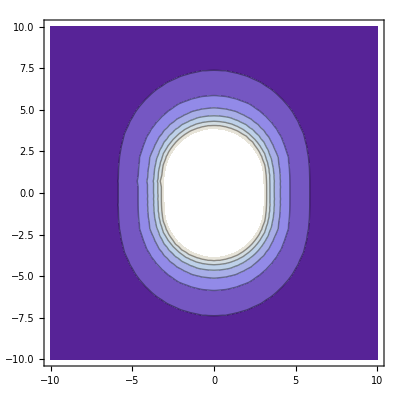

```mathematica
ContourPlot[NormCyl[{Brm[Sqrt[R^2+Z^2],ArcTan[R/Z]],0,Bzm[Sqrt[R^2+Z^2],ArcTan[R/Z]]}],{R,-10,10},{Z,-10,10}]
```

And the direction doesn’t look half bad

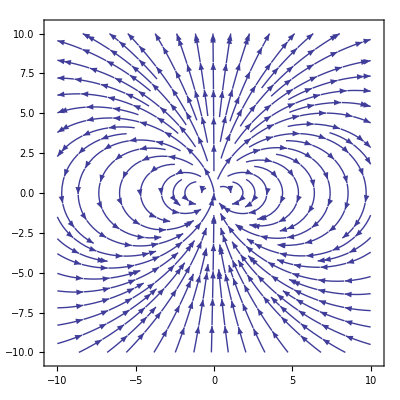

```mathematica
StreamPlot[RandZ[{Brm[Sqrt[R^2+Z^2],ArcTan[R/Z]],0,Bzm[Sqrt[R^2+Z^2],ArcTan[R/Z]]}],{R,-10,10},{Z,-10,10}]
```

## Magnetic field of a disc

#### The field at a vector v from a cylinder (with diameter d and height h and magnetization M=m x Volume) at the origin is a sum of dipoles situated at varying {r,θ,z}

Bd[v_,m_:1,d_,h_]:=∫_(-d/2)^(d/2) ∫_(-h/2)^(h/2) ∫_0^π Bm[VecDiff[v,{r,θ,z}],m]jdet ⅆθⅆzⅆr

or maybe I should do it numerically, 
return 0 if within disk 
all dimensions are in mm
m=1050 fits best to the fields given by manufacturer

```mathematica
NBd[{R_,Φ_,ZZ_},m_:1,d_:7.5,h_:2.5]:=
Piecewise[{{0,-d/2≤R≤d/2 && -h/2≤ZZ≤h/2}},
With[{rm=(r^2+R^2-2r R Cos[ϕ])^(1/2),zm=ZZ-z,ϕm=ArcTan[R-r Cos[ϕ],r Sin[ϕ]]},
With[{v=(rm^2+zm^2)^(1/2),θ=ArcTan[rm/zm]},
With[{Bdz=NIntegrate[2Bzm[v,θ,m]jdet ,{ϕ,0,π},{r,0,d/2},{z,-h/2,h/2},AccuracyGoal->5],
Bdr=NIntegrate[2 Cos[ϕm]Brm[v,θ,m]jdet ,{ϕ,0,π},{r,0,d/2},{z,-h/2,h/2},AccuracyGoal->5]},
{Bdr ,Φ,Bdz}]
]
]
]
```

(m=1050 fits best to the fields given by manufacturer) all lengths in mm and field in G

```mathematica
Chop[NBd[{0,0,#+1.25},1050,7.5,2.5]]&/@ {1,10,100}
```

{{0,0,2801.6},{0,0,141.824},{0,0,0.223062}}

This is just to compare approximating the disk as a dipole

```mathematica
NBm[{R_,Φ_,Zz_},m_:1050,d_:7.5,h_:2.5]:=
Piecewise[{{0,-d/2≤R≤d/2 && -h/2≤Zz≤h/2}},
With[{rm=R,zm=Zz,M=  ∫_0^(d/2) ∫_(-h/2)^(h/2) ∫_0^(2π) m jdet ⅆϕⅆzⅆr},
With[{v=(rm^2+zm^2)^(1/2),θ=ArcTan[rm/zm]},
{Brm[v,θ,M],Φ,Bzm[v,θ,M]}]
]
]
```

Approximating the disk as a dipole is > 95% accurate for z > ~18mm

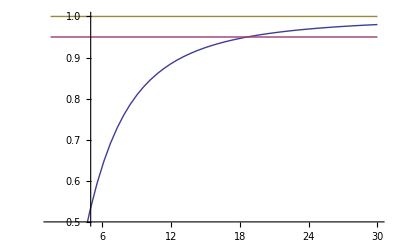

```mathematica
Plot[{NBd[{0,0,Z}]⟦3⟧/NBm[{0,0,Z}]⟦3⟧,0.95,1},{Z,1.5,30},PlotRange->{0.5,1}]
```

## Field in Cartesian Coordinates, at a given point in Cartesian space

```mathematica
NBdCartesian[{x_,y_,z_}]:=CoordinatesToCartesian[NBd[CoordinatesFromCartesian[{x,y,z},Cylindrical]],Cylindrical]
```

## Field in Spherical Coordinates, at a given point in Cartesian space

The definition of spherical here is the one given by the vector analysis package. this matches with NVsim now.

```mathematica
NBdSpherical[{x_,y_,z_}]:=CoordinatesFromCartesian[NBdCartesian[{x,y,z}],Spherical]
```

```mathematica
NBdSpherical[{x_,y_,z_},m_]:={m,1,1}NBdSpherical[{x,y,z}]
```

## Some examples

```mathematica
T=Table[NBd[{R,0,Z}],{R,0,20,1},{Z,0,30,1}];
```

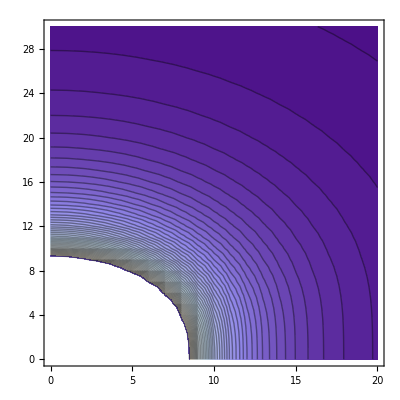

```mathematica
ampplot=ListContourPlot[Table[NormCyl[T[[j,k]]],{k,1,31,1},{j,1,21,1}],Contours->Range[0,10,.005],DataRange->{{0,20},{0,30}}]
```

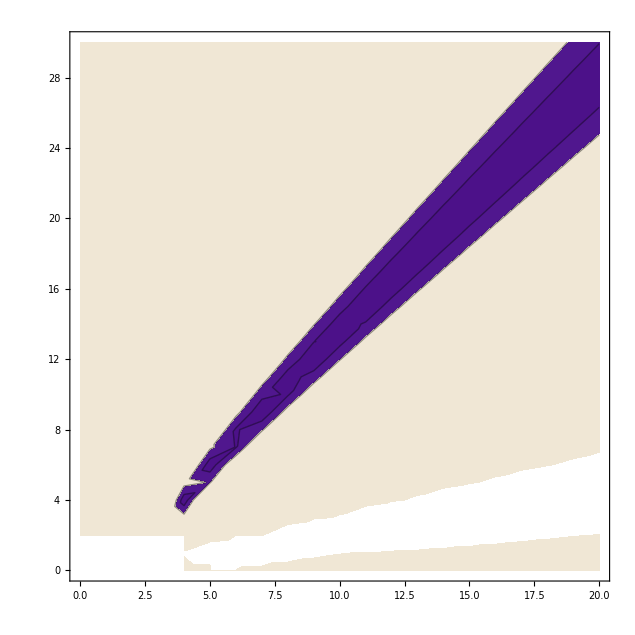

```mathematica
angleplot=ListContourPlot[Table[Abs[Tan[Angle[T[[j,k]]]-.955]],{k,1,31,1},{j,1,21,1}],Contours->Range[0,.1,.05],DataRange->{{0,20},{0,30}}]
```

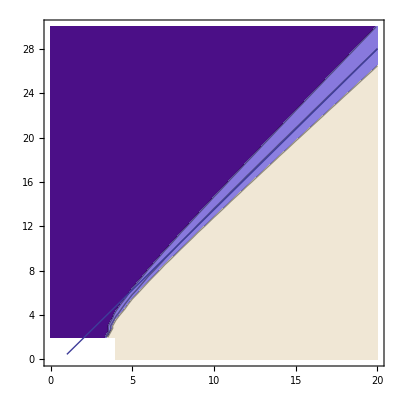

```mathematica
Show[angleplot,Plot[1.45 x-1,{x,1,20}]]
```

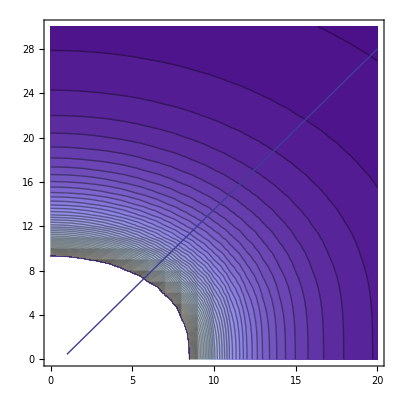

```mathematica
Show[ampplot,Plot[1.45 x-1,{x,1,20}]]
```

```mathematica
1.45*2
```

2.9

Plot the magnitude of the field as a function of radial distance at various heights from surface of magnet.

```mathematica
NBd[{0,0,4.2+#}]&/@{15.5,20.5,25}//Chop
```

{{0,0,28.9746},{0,0,14.9469},{0,0,9.12225}}

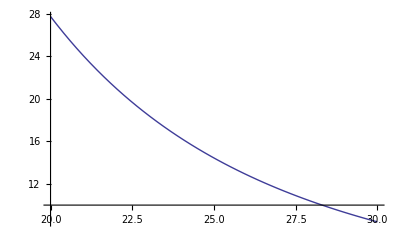

```mathematica
Plot[NormCyl[NBd[{0,0,z}]],{z,20,30},PlotRange->Automatic]
```

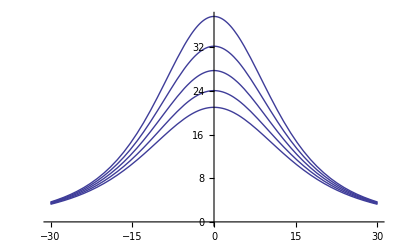

```mathematica
Plot[NormCyl[NBd[{R,0,#}]]&/@{18,19,20,21,22},{R,-30,30},PlotRange->Automatic]
```

and angle

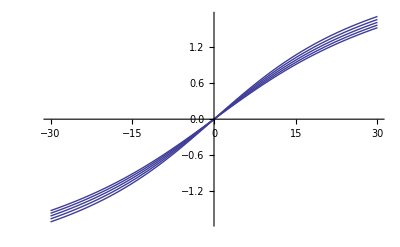

```mathematica
Plot[Angle[NBd[{R,0,#}]]&/@{18,19,20,21,22},{R,-30,30},PlotRange->Automatic]
```